```mathematica
img=Import["~/Dropbox/projects/pigun/testimgs/flp/img2.png"];
tmp=ImageData[img];
Length[tmp]
Length[tmp[[1]]]
img=ImageResize[img,{Length[tmp[[1]]]/2,Length[tmp]/2}];
img=ImageData[img];
img=0.299img[[All,All,1]]+0.587img[[All,All,2]]+0.114img[[All,All,3]];
```

720

1280

```mathematica
MatrixPlot[img,ColorFunction->GrayLevel]
```

-Graphics-

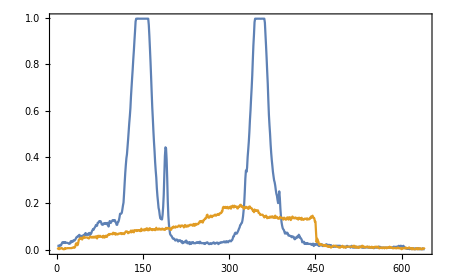

```mathematica
ListPlot[img[[{130,200}]],PlotRange->All]
```

```mathematica
ny=Length[img[[1]]];
nx=Length[img];
peaks={{-1,1,0,0,0},{-1,ny,0,0,0}};
t=0.5;

For[i=1,i≤nx,i++,(* i/x is for rows *)

status=0;
linesumx=0;
linesumy=0;

For[j=1,j≤ny,j++,(* j/y is for columns *)

If[status<0,
status++;
Continue[];
];

px=img[[i,j]];

If[px>t && status==0,(* start recording the histogram *)
status=1;
linesumy=0;linesumx=0;
];
If[px>t && status==1,(* record the histogram *)
linesumx+=px;
linesumy+=px*j;
];
If[px≤t && status==1, (* stop recording, peak ended *)
status=-5;(* enable record starting again after 5 pixels at least *)
(* store the partial result somewhere *)
total=linesumx;
(*linesumx*=i/total;
linesumy/=total;*)
thisY=linesumy/total;

(*Print[{"peak done:",i,linesumx,linesumy}];*)
(* update info in pID? *)
(* which peak is the closest in y to the *)
dists={0,0};
dists[[1]]=Abs[peaks[[1,2]]-thisY];
dists[[2]]=Abs[peaks[[2,2]]-thisY];
If[dists[[1]]<dists[[2]],pID=1;,pID=2;];(* get the closest peak *)
peaks[[pID,3]]+=total;
peaks[[pID,4]]+=linesumx*i;
peaks[[pID,5]]+=linesumy;
peaks[[pID,2]]=thisY;

];


];(* end of loop over j *)

];(* end of loop over i *)
peaks[[All,1]]=peaks[[All,4]]/peaks[[All,3]]
peaks[[All,2]]=peaks[[All,5]]/peaks[[All,3]]
peaks
```

{132.402,125.412}

{148.023,352.915}

{{132.402,148.023,1114.19,147522.,164926.},{125.412,352.915,853.761,107072.,301305.}}

```mathematica
tmp=peaks[[All,{2,1}]];
tmp={#[[1]],(360-#[[2]])}&/@tmp;
Show[{ListDensityPlot[Reverse[img]]
,ListPlot[tmp,Joined->False,PlotStyle->Red]
}]
```

-Graphics-